# Muon Beam Dump: BSM Scalar with FeynCalc

#### Notebook Description:

In this notebook, we go through calculations of cross sections for the production of beyond the Standard Model (BSM) states in a muon beam dump experiment, through scattering of the form
μ^-N → μ^- N ϕ_BSM
where ϕ_BSM indicates a BSM scalar.

We set up the relevant definitions and typesetting in Setup and perform calculations in Beam Dump Calculations.

Details:

In Beam Dump Calculations, we calculate cross sections for the full 2→3 process. Our calculations use FeynCalc, and rely on a model we design in the format of FeynRules and load using FeynArts.

# Setup

Setting up directories

```mathematica
$DirectorySetup="/Users/sam/Documents/Research/BeamDumpBSM/setup/directories.m";
Get[$DirectorySetup]
```

### FeynCalc, Models, Typesetting

#### Loading FeynCalc and FeynArts

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True];
```

Successfully patched FeynArts.

#### Initializing and Typesetting Model

Nuclide Specific Typesetting

```mathematica
MakeBoxes[FFnuclidefermion,TraditionalForm]:=" \!\(\*SubscriptBox[\(F\), fermion]\)(q) ";
MakeBoxes[FFnuclidescalar,TraditionalForm]:=" \!\(\*SubscriptBox[\(F\), scalar]\)(q) ";
```

```mathematica
MakeBoxes[Pprime,TraditionalForm]:="\!\(\*P'\)";
```

Model Independent

```mathematica
MakeBoxes[epsel,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), e]\)";
MakeBoxes[epsmu,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), \(μ\)]\)";
```

Model Specific

```mathematica
InitializeModel["scalar_mubeamdump"];
```

loading generic model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/scalar_mubeamdump.mod

> 14 particles (incl. antiparticles) in 8 classes

> $CounterTerms are ON

> 7 vertices

classes model {scalar_mubeamdump} initialized

Names, couplings, etc

```mathematica
MakeBoxes[mBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(X\)]\)";

MakeBoxes[gel,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), e]\)";
MakeBoxes[gmu,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), \(μ\)]\)";

MakeBoxes[yphie,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), e]\)";
MakeBoxes[yphimu,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), \(μ\)]\)";
```

Kinematic Properties of the BSM final state:

```mathematica
MakeBoxes[EBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(X\)]\)";
MakeBoxes[betaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(β\), \(X\)]\)";
MakeBoxes[thetaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(θ\), \(X\)]\)";
```

#### Other Typesetting

Outgoing lepton:

```mathematica
MakeBoxes[pprime,TraditionalForm]:="\!\(\*p'\)";
```

Beam and Target:

```mathematica
MakeBoxes[E0,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(0\)]\)";
MakeBoxes[Mi,TraditionalForm]:="\!\(\*SubscriptBox[\(M\), \(Target\)]\)";
```

SM Parameters:

```mathematica
MakeBoxes[mu,TraditionalForm]:="\!\(\*SubscriptBox[\(μ\)]\)";

MakeBoxes[mel,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), e]\)";
MakeBoxes[mmu,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(μ\)]\)";

MakeBoxes[alphaEM,TraditionalForm]:="\!\(\*SubscriptBox[\(α\), EM]\)";
```

#### Replacement Rules

```mathematica
BeamDumpCouplingRules = {gel->epsel e,gmu->epsmu e,e^2->4π alphaEM};
```

### 2→3 Kinematics

#### On - Shell Setup

```mathematica
SP[p,p]=mmu^2;
SP[pprime,pprime]=mmu^2;
SP[k,k]=mBSM^2;
```

```mathematica
SP[P,P]=Mi^2;
SP[Pprime,Pprime]=Mi^2;
```

#### Kinematic Variable Setup

Nucleon-Lepton

```mathematica
SP[P,p]=1/2(s-mmu^2-Mi^2);
```

Nucleon-Nucleon

Let’s work in the elastic limit, since inelastic contributions are expected to be suppressed anyway
			P = P' + q
			⇒
			P^2 - 2 P.P' + (P')^2 = q^2=-Q^2
			⇒
			2 P.P' = Q^2+P^2+(P')^2

```mathematica
SP[P,Pprime]=Q^2/2+Mi^2;
```

#### “Limit Checker” Replacement Rules:

```mathematica
AllMassless = {mel->0,mmu->0,mBSM ->0,
(* also, zero virtuality for the WW photon: *)
SP[q,q]->0,SP[q,q]^2->0};
```

# Beam Dump Calculations

## 2→3 Calculation

### (Squared) Amplitude

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

> Top. 13: 0 Classes insertions

> Top. 14: 0 Classes insertions

> Top. 15: 0 Classes insertions

> Top. 16: 0 Classes insertions

> Top. 17: 0 Classes insertions

> Top. 18: 0 Classes insertions

> Top. 19: 0 Classes insertions

> Top. 20: 1 Classes insertion

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 0 Classes insertions

> Top. 25: 1 Classes insertion

in total: 2 Classes insertions

> Top. 1 afbg/chdfeg/fhgh.m, 0 diagrams

> Top. 2 afbg/chdheg/fgfh.m, 0 diagrams

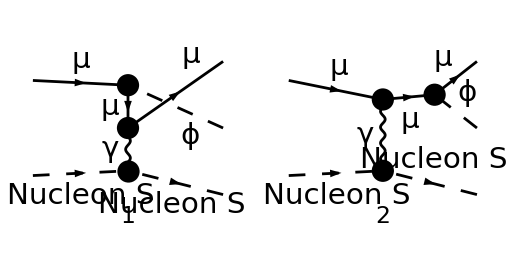

```mathematica
diagrams2to3= InsertFields[CreateTopologies[0, 2 -> 3], {F[2],S[9]} ->
		{F[2],S[1],S[9]}, InsertionLevel -> {Classes}, Model->{"scalar_mubeamdump"}];
Paint[diagrams2to3, ColumnsXRows -> {2, 1}, Numbering -> Simple,
	SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amplitude=FCFAConvert[CreateFeynAmp[diagrams2to3], IncomingMomenta->{p,P},
	OutgoingMomenta->{pprime,k, Pprime},UndoChiralSplittings->True,ChangeDimension->4, List->False, SMP->True,
	Contract->True];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

```mathematica
amplitudeSquared = (amplitude (ComplexConjugate[amplitude]))//
FeynAmpDenominatorExplicit// 
FermionSpinSum[#, ExtraFactor -> 1/2 (* Averaging over initial l.00epton polarizations *)]&//
DiracSimplify//
FullSimplify;
```

$Aborted

```mathematica
amplitudeSquared = (amplitude (ComplexConjugate[amplitude]))//
FeynAmpDenominatorExplicit// 
FermionSpinSum[#, ExtraFactor -> 1/2 (* Averaging over initial l.00epton polarizations *)]&//
DiracSimplify
```

-(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (OverBar[p']·OverBar[P'])^2 e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(8 (F_scalar(q))^2 y_μ^2 (k̄·p̄) (OverBar[p']·OverBar[P'])^2 e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 s y_μ^2 (OverBar[p']·OverBar[P'])^2 e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 M_Target^2 y_μ^2 (OverBar[p']·OverBar[P'])^2 e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (OverBar[p']·OverBar[P'])^2 e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 y_μ^2 (p̄·OverBar[p']) (OverBar[p']·OverBar[P'])^2 e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 m_μ^2 s y_μ^2 (k̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 m_μ^4 y_μ^2 (k̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (k̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(4 (F_scalar(q))^2 s y_μ^2 (k̄·OverBar[p']) (k̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(4 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·OverBar[p']) (k̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(4 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·OverBar[p']) (k̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(2 (F_scalar(q))^2 m_X^2 y_μ^2 (p̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 m_μ^2 y_μ^2 (p̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p']))^2)+(8 (F_scalar(q))^2 m_X^2 M_Target^2 y_μ^2 (p̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(32 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (p̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·OverBar[P']) (p̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(8 (F_scalar(q))^2 y_μ^2 (k̄·OverBar[p']) (k̄·OverBar[P']) (p̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·P̄) (p̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(8 (F_scalar(q))^2 y_μ^2 (k̄·P̄) (k̄·OverBar[p']) (p̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(4 (F_scalar(q))^2 m_X^2 y_μ^2 (p̄·OverBar[P']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (p̄·OverBar[P']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(2 (F_scalar(q))^2 m_X^2 s y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(8 (F_scalar(q))^2 m_μ^2 s y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 m_μ^4 y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(2 (F_scalar(q))^2 m_X^2 M_Target^2 y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(2 (F_scalar(q))^2 m_X^2 m_μ^2 y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(4 (F_scalar(q))^2 m_X^2 y_μ^2 (p̄·OverBar[P']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (p̄·OverBar[P']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·OverBar[P']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 y_μ^2 (k̄·OverBar[P']) (p̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 y_μ^2 (k̄·P̄) (p̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (p̄·OverBar[P']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(16 (F_scalar(q))^2 y_μ^2 (k̄·P̄) (p̄·OverBar[P']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 y_μ^2 (k̄·OverBar[p']) (p̄·OverBar[P']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(32 (F_scalar(q))^2 m_μ^2 y_μ^2 (P̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(16 (F_scalar(q))^2 y_μ^2 (k̄·p̄) (P̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 m_μ^2 s y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(8 (F_scalar(q))^2 m_μ^2 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(8 (F_scalar(q))^2 m_μ^4 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(40 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(4 (F_scalar(q))^2 y_μ^2 (k̄·p̄) (OverBar[p']·OverBar[P']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·p̄) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(8 (F_scalar(q))^2 s y_μ^2 (k̄·P̄) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·P̄) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·P̄) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(4 (F_scalar(q))^2 s y_μ^2 (k̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(4 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(4 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(2 (F_scalar(q))^2 m_X^2 s y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(8 (F_scalar(q))^2 m_μ^2 s y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 m_μ^4 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(2 (F_scalar(q))^2 m_X^2 M_Target^2 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(2 (F_scalar(q))^2 m_X^2 m_μ^2 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(4 (F_scalar(q))^2 s y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^2 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 M_Target^2 s y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(4 (F_scalar(q))^2 M_Target^2 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^2 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(4 (F_scalar(q))^2 m_μ^2 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^2 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(8 (F_scalar(q))^2 M_Target^4 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(8 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (OverBar[p']·OverBar[P']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(16 (F_scalar(q))^2 M_Target^2 y_μ^2 (p̄·OverBar[P']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(8 (F_scalar(q))^2 s y_μ^2 (P̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 M_Target^2 y_μ^2 (P̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(24 (F_scalar(q))^2 m_μ^2 y_μ^2 (P̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(16 (F_scalar(q))^2 y_μ^2 (p̄·OverBar[p']) (P̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(16 (F_scalar(q))^2 y_μ^2 (p̄·OverBar[P']) (P̄·OverBar[p']) (OverBar[p']·OverBar[P']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (P̄·OverBar[p'])^2 e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(8 (F_scalar(q))^2 y_μ^2 (k̄·p̄) (P̄·OverBar[p'])^2 e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(4 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·OverBar[P']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(16 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (k̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(4 (F_scalar(q))^2 y_μ^2 (k̄·OverBar[P']) (p̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(16 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·OverBar[P']) (p̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(4 (F_scalar(q))^2 y_μ^2 (k̄·P̄) (p̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·P̄) (p̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 m_μ^2 y_μ^2 (p̄·OverBar[P']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(32 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (p̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(4 (F_scalar(q))^2 y_μ^2 (k̄·OverBar[p']) (p̄·OverBar[P']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·OverBar[p']) (p̄·OverBar[P']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 s y_μ^2 (k̄·OverBar[P']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(8 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·OverBar[P']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 y_μ^2 (k̄·OverBar[P']) (p̄·OverBar[p']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 y_μ^2 (k̄·P̄) (p̄·OverBar[p']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 y_μ^2 (k̄·OverBar[P']) (p̄·OverBar[P']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 m_μ^2 y_μ^2 (p̄·OverBar[P']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 y_μ^2 (k̄·OverBar[p']) (p̄·OverBar[P']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 m_μ^2 s y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 m_μ^2 y_μ^2 (P̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(8 (F_scalar(q))^2 m_μ^4 y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(24 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(4 (F_scalar(q))^2 y_μ^2 (k̄·p̄) (P̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(16 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·p̄) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·P̄) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(4 (F_scalar(q))^2 s y_μ^2 (k̄·OverBar[p']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(4 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·OverBar[p']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(4 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·OverBar[p']) (P̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(4 (F_scalar(q))^2 m_μ^2 s y_μ^2 e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(16 (F_scalar(q))^2 M_Target^2 m_μ^2 s y_μ^2 e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(4 (F_scalar(q))^2 m_μ^4 y_μ^2 e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(4 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 M_Target^2 m_μ^4 y_μ^2 e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 M_Target^4 m_μ^2 y_μ^2 e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(4 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·P̄) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(16 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (k̄·P̄) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(2 (F_scalar(q))^2 s y_μ^2 (k̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(8 (F_scalar(q))^2 M_Target^2 s y_μ^2 (k̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(2 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(2 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 M_Target^4 y_μ^2 (k̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))-(8 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (k̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p'])) (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P'])))+(8 (F_scalar(q))^2 m_μ^4 y_μ^2 e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p']))^2)+(2 (F_scalar(q))^2 m_X^2 m_μ^2 y_μ^2 e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p']))^2)+(32 (F_scalar(q))^2 M_Target^2 m_μ^4 y_μ^2 e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(8 (F_scalar(q))^2 m_X^2 M_Target^2 m_μ^2 y_μ^2 e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·p̄) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p']))^2)-(32 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (k̄·p̄) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(8 (F_scalar(q))^2 m_μ^2 s y_μ^2 (k̄·P̄) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 m_μ^4 y_μ^2 (k̄·P̄) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(8 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (k̄·P̄) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(8 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p']))^2)+(32 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (k̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(4 (F_scalar(q))^2 y_μ^2 (k̄·p̄) (k̄·OverBar[p']) e^4)/(Q^2 (m_X^2+2 (k̄·OverBar[p']))^2)-(16 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·p̄) (k̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)+(4 (F_scalar(q))^2 s y_μ^2 (k̄·P̄) (k̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(4 (F_scalar(q))^2 M_Target^2 y_μ^2 (k̄·P̄) (k̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(4 (F_scalar(q))^2 m_μ^2 y_μ^2 (k̄·P̄) (k̄·OverBar[p']) e^4)/(Q^4 (m_X^2+2 (k̄·OverBar[p']))^2)-(2 (F_scalar(q))^2 m_μ^2 y_μ^2 e^4)/((Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(8 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 e^4)/(Q^2 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 m_μ^2 y_μ^2 (P̄·OverBar[p'])^2 e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 y_μ^2 (p̄·OverBar[p']) (P̄·OverBar[p'])^2 e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(16 (F_scalar(q))^2 y_μ^2 (p̄·OverBar[P']) (P̄·OverBar[p'])^2 e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(2 (F_scalar(q))^2 y_μ^2 (p̄·OverBar[p']) e^4)/((Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(8 (F_scalar(q))^2 M_Target^2 y_μ^2 (p̄·OverBar[p']) e^4)/(Q^2 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)-(8 (F_scalar(q))^2 M_Target^2 s y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 M_Target^4 y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 M_Target^2 m_μ^2 y_μ^2 (P̄·OverBar[p']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(8 (F_scalar(q))^2 y_μ^2 (p̄·OverBar[P']) (P̄·OverBar[p']) e^4)/(Q^2 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)+(16 (F_scalar(q))^2 M_Target^2 y_μ^2 (p̄·OverBar[P']) (P̄·OverBar[p']) e^4)/(Q^4 (Q^2+2 (P̄·OverBar[p'])-2 (OverBar[p']·OverBar[P']))^2)

### Applying Standard Formulae for dσ/dx in the Lab Frame

#### Setting up 2→2 Differential Cross Sections

Off-Shell

```mathematica
var["dσ/dt_2"] = amplitudeSquared/(16π stilde^2)//.BeamDumpCouplingRules//.TwoToTildeMu//TrickMandelstam[#,{stilde,t2,utilde,q^2+mBSM^2}]&//FullSimplify;
var["dσ/(d (p . k))"] = 2var["dσ/dt_2"];
var["A^(2 → 2)"]=(stilde^2 var["dσ/(d (p . k))"])/(2π epsmu^2 alphaEM^2);
```

On-Shell

```mathematica
var["dσ/(d (p . k)) on-shell"] = var["dσ/(d (p . k))"]/.q^2->0;
var["A^(2 → 2) on-shell"]=(stilde^2 var["dσ/(d (p . k)) on-shell"])/(2π epsmu^2 alphaEM^2);
```

#### Explicit Expressions

Off-shell

```mathematica
var["dσ/dt_2"]
```

-1/((s̃)^4 (ũ)^2)2 π α_EM^2 ϵ_μ^2 (2 m_μ^2 (q^2 (3 (s̃)^2-4 s̃ ũ+3 (ũ)^2)+6 s̃ ũ (s̃+ũ))-m_X^2 (q^2 ((s̃)^2-4 s̃ ũ+(ũ)^2)+2 m_μ^2 ((s̃)^2+8 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))+s̃ ũ ((s̃)^2-2 q^2 (s̃+ũ)+(ũ)^2+2 q^4)+12 m_μ^4 (s̃+ũ)^2+2 s̃ ũ m_X^4)

```mathematica
var["dσ/(d (p . k))"]
```

-1/((s̃)^4 (ũ)^2)4 π α_EM^2 ϵ_μ^2 (2 m_μ^2 (q^2 (3 (s̃)^2-4 s̃ ũ+3 (ũ)^2)+6 s̃ ũ (s̃+ũ))-m_X^2 (q^2 ((s̃)^2-4 s̃ ũ+(ũ)^2)+2 m_μ^2 ((s̃)^2+8 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))+s̃ ũ ((s̃)^2-2 q^2 (s̃+ũ)+(ũ)^2+2 q^4)+12 m_μ^4 (s̃+ũ)^2+2 s̃ ũ m_X^4)

```mathematica
var["A^(2 → 2)"]
```

-1/((s̃)^2 (ũ)^2)2 (2 m_μ^2 (q^2 (3 (s̃)^2-4 s̃ ũ+3 (ũ)^2)+6 s̃ ũ (s̃+ũ))-m_X^2 (q^2 ((s̃)^2-4 s̃ ũ+(ũ)^2)+2 m_μ^2 ((s̃)^2+8 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))+s̃ ũ ((s̃)^2-2 q^2 (s̃+ũ)+(ũ)^2+2 q^4)+12 m_μ^4 (s̃+ũ)^2+2 s̃ ũ m_X^4)

On-shell

```mathematica
var["dσ/(d (p . k)) on-shell"]
```

-1/((s̃)^4 (ũ)^2)4 π α_EM^2 ϵ_μ^2 (s̃ ũ ((s̃)^2+(ũ)^2+2 q^4)-m_X^2 (2 m_μ^2 ((s̃)^2+8 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))+12 m_μ^4 (s̃+ũ)^2+12 s̃ ũ m_μ^2 (s̃+ũ)+2 s̃ ũ m_X^4)

```mathematica
var["A^(2 → 2) on-shell"]
```

-1/((s̃)^2 (ũ)^2)2 (s̃ ũ ((s̃)^2+(ũ)^2+2 q^4)-m_X^2 (2 m_μ^2 ((s̃)^2+8 s̃ ũ+(ũ)^2)+2 s̃ ũ (s̃+ũ))+12 m_μ^4 (s̃+ũ)^2+12 s̃ ũ m_μ^2 (s̃+ũ)+2 s̃ ũ m_X^4)

### Applying Kinematic Approximations

#### Stating Approximations:

```mathematica
tMinApproximations = {
stilde->-utilde/(1-x),
utilde->-x E0^2 thetaBSM^2-mBSM^2(1-x)/x-mmu^2 x,
t2->(utilde x)/(1-x)+mBSM^2,
SP[q,q]->-stilde^2/(4 E0^2)
};
```

#### Applying Approximations

Off-shell

```mathematica
var["dσ/(d (p . k)) near tmin"] =var["dσ/(d (p . k))"]//.tMinApproximations//FullSimplify;
```

```mathematica
var["A^(2 → 2) near tmin"]=(stilde^2 var["dσ/(d (p . k)) near tmin"])/(2π epsmu^2 alphaEM^2)//.tMinApproximations//FullSimplify;
```

On-shell

```mathematica
var["dσ/(d (p . k)) on-shell near tmin"] =var["dσ/(d (p . k)) on-shell"]//.tMinApproximations//FullSimplify;
```

```mathematica
var["A^(2 → 2) on-shell near tmin"]=(stilde^2 var["dσ/(d (p . k)) on-shell near tmin"])/(2π epsmu^2 alphaEM^2)//.tMinApproximations//FullSimplify;
```

#### Explicit Expressions

Off-Shell

```mathematica
var["dσ/(d (p . k)) near tmin"]
```

-((π α_EM^2 ϵ_μ^2 x^2 (2 E_0^2 (4 q^4 (x-1)^3 x^2+m_μ^4 x^4 (θ_X^2 ((20-9 x) x-20)+2 (x-1) ((x-2) x+2))+m_X^4 (-(x-1)) (x (θ_X^2 x ((x-3) x+3)-2 x ((x-4) x+7)+12)-4)+m_μ^2 m_X^2 x^2 (θ_X^2 (x (x (x (x+6)-26)+40)-20)-4 (x-1)^2 ((x-2) x+2)))-2 E_0^6 θ_X^4 x^4 (x (x (θ_X^2-2 x+6)-8)+4)+E_0^4 θ_X^2 x^2 (4 m_μ^2 x^2 (θ_X^2 ((5-3 x) x-5)+2 (x-1) ((x-8) x+8))+m_X^2 (x (x (x (θ_X^2 x+16)-48)+48)-16))+(m_X^2 (x-1)-m_μ^2 x^2)^2 (m_X^2 (x-2)^2-4 m_μ^2 (x (2 x-5)+5))))/(E_0^2 (m_X^2 (x-1)-x^2 (E_0^2 θ_X^2+m_μ^2))^4))

```mathematica
var["A^(2 → 2) near tmin"]//FullSimplify
```

-((2 E_0^2 (4 q^4 (x-1)^3 x^2+m_μ^4 x^4 (θ_X^2 ((20-9 x) x-20)+2 (x-1) ((x-2) x+2))+m_X^4 (-(x-1)) (x (θ_X^2 x ((x-3) x+3)-2 x ((x-4) x+7)+12)-4)+m_μ^2 m_X^2 x^2 (θ_X^2 (x (x (x (x+6)-26)+40)-20)-4 (x-1)^2 ((x-2) x+2)))-2 E_0^6 θ_X^4 x^4 (x (x (θ_X^2-2 x+6)-8)+4)+E_0^4 θ_X^2 x^2 (4 m_μ^2 x^2 (θ_X^2 ((5-3 x) x-5)+2 (x-1) ((x-8) x+8))+m_X^2 (x (x (x (θ_X^2 x+16)-48)+48)-16))+(m_X^2 (x-1)-m_μ^2 x^2)^2 (m_X^2 (x-2)^2-4 m_μ^2 (x (2 x-5)+5)))/(2 (E_0-E_0 x)^2 (m_X^2 (x-1)-x^2 (E_0^2 θ_X^2+m_μ^2))^2))

On-shell

```mathematica
var["dσ/(d (p . k)) on-shell near tmin"]
```

-((4 π α_EM^2 ϵ_μ^2 (x-1) x^2 (2 q^4 (x-1)^2 x^2-2 m_X^2 (x-1) x^2 (m_μ^2 ((x-2) x+2)-2 E_0^2 θ_X^2 (x-1))+x^4 (E_0^4 θ_X^4 ((x-2) x+2)+2 E_0^2 θ_X^2 m_μ^2 ((x-8) x+8)+m_μ^4 ((x-2) x+2))+m_X^4 (x-1)^2 ((x-2) x+2)))/(m_X^2 (x-1)-x^2 (E_0^2 θ_X^2+m_μ^2))^4)

```mathematica
var["A^(2 → 2) on-shell near tmin"]//FullSimplify
```

-((2 (2 q^4 (x-1)^2 x^2-2 m_X^2 (x-1) x^2 (m_μ^2 ((x-2) x+2)-2 E_0^2 θ_X^2 (x-1))+x^4 (E_0^4 θ_X^4 ((x-2) x+2)+2 E_0^2 θ_X^2 m_μ^2 ((x-8) x+8)+m_μ^4 ((x-2) x+2))+m_X^4 (x-1)^2 ((x-2) x+2)))/((x-1) (m_X^2 (x-1)-x^2 (E_0^2 θ_X^2+m_μ^2))^2))

# Saving Results

Putting everything into a single function

# Saving Results

Putting everything into a single function

```mathematica
var["Squared, Spin-Averaged Matrix Element"]=amplitudeSquared;
var["Squared, Spin-Averaged Matrix Element on-shell"]=amplitudeSquared//.SP[q,q]->0;
```

```mathematica
keys = {"Squared, Spin-Averaged Matrix Element",
"Squared, Spin-Averaged Matrix Element on-shell",
"dσ/(d (p . k))", "dσ/(d (p . k)) on-shell",
"dσ/(d (p . k)) near tmin", "dσ/(d (p . k)) on-shell near tmin",
"A^(2 → 2)", "A^(2 → 2) on-shell",
"A^(2 → 2) near tmin", "A^(2 → 2) on-shell near tmin"};
```

```mathematica
Do[pseudovector2to2[keys[[i]]]=var[keys[[i]]],{i,Length[keys]}]

(* For debugging: *)
(*pseudovector2to2/@keys*)
```

Saving all functions

```mathematica
Put[FullDefinition[pseudovector2to2],$pseudovector2to2Functions]
```

```mathematica
PutAppend[FullDefinition[tMinApproximations], $pseudovector2to2Functions]
```

```mathematica
Quit[]
```